```mathematica
R[x_,y_]:=Sqrt[x^2+y^2]
earth=Graphics[{PointSize[0.055] ,ColorData[97,"ColorList"][[1]],Point[{0,0}]}];
```

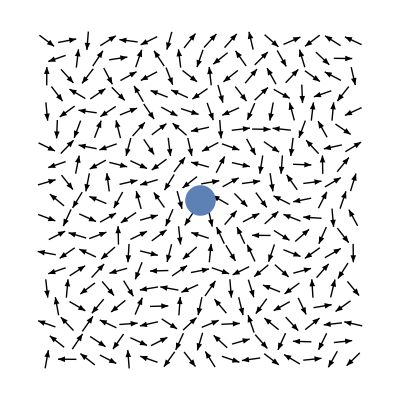

```mathematica
img =Show[{
VectorPlot[RandomVariate[NormalDistribution[],2],{x,-3,3},{y,-3,3},Frame->False,VectorColorFunction->None,VectorStyle->Black],
earth
}]
Export["gw_orientation_iso.pdf",img];
```

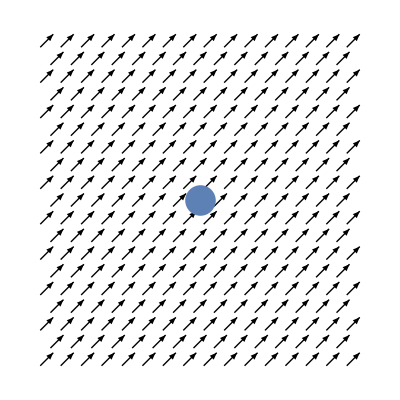

```mathematica
img=Show[{
VectorPlot[{1,1},{x,-3,3},{y,-3,3},Frame->False,VectorColorFunction->None,VectorStyle->Black],
earth
}]
Export["gw_orientation_dip.pdf",img];
```

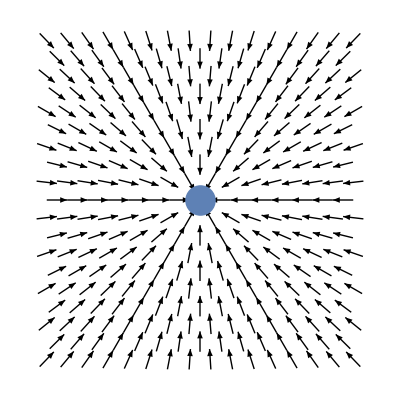

```mathematica
img = Show[{
VectorPlot[{-x/R[x,y],-y/R[x,y]},{x,-3,3},{y,-3,3},Frame->False,VectorColorFunction->None,VectorStyle->Black],
earth
}]
Export["gw_orientation_inc.pdf",img];
```